```mathematica
(*σ represents loss and my hashing rate is a function of σ and ν, my displacement (postselection window) and i want to display a plot of the length of my chains and the hashing rate, where I change my values of σ, to represent different values of "σ_threshold".

I have already calculated the hashing rate for all values of σ and ν for chains of different lengths, but now I want to pick a value of σ which we consider σ threshold and we maximise ν*)


(*Starting from the code we already have to make our chains we generate all the chains first*)

(*Partial Trace Code*)
(*system, subsystem(s) being traced out, dimensions of subsystems*)
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
dTraceSystem[D_, s_, dimen_]:=Module[{Qudits,TrkM,dim,z,q,n,M,k,p,j,b,i,c,perm}, (

Qudits=Reverse[Sort[s]];
TrkM=D;
dim=dimen;

z=(Dimensions[Qudits][[1]]+1);

For[q=1,q<z,q++,
n=Log[dim,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qudits[[q]];
If[k==n,
TrkM={};
For[p=1,p<dim^n+1,p=p+dim,
TrkM=Append[TrkM,∑_(h=0)^(dim-1) Take[M[[p+h,All]],{1+h,dim^n,dim}]];
 ],

For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<dim^n+1,i++,
If[IntegerDigits[i-1,dim,n][[n]]≠IntegerDigits[i-1,dim,n][[n-j-1]] && Count[b, i]  ==0, 
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,dim, n]),{n},{n-j-1}],dim]+1)];
c=Range[dim^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,dim, n]),{n},{n-j-1}],dim]+1)}];
M=M[[perm,perm]];
 ]    
];
   ];

TrkM={};
For[p=1,p<dim^n+1,p=p+dim,
TrkM=Append[TrkM,∑_(h=0)^(dim-1) Take[M[[p+h,All]],{1+h,dim^n,dim}]];
]
]
]

;Return[TrkM])
]
(*Defining basic variables*)

zero = {{1} , {0}};
one = {{0} , {1}};

ϕplus =( KroneckerProduct[zero , zero]+KroneckerProduct[one , one])/Sqrt[2];
ϕminus = ( KroneckerProduct[zero , zero]-KroneckerProduct[one , one])/Sqrt[2];
ψplus = ( KroneckerProduct[zero , one]+KroneckerProduct[one , zero])/Sqrt[2];
ψminus = ( KroneckerProduct[zero , one]-KroneckerProduct[one , zero])/Sqrt[2];

Φplus = ϕplus.ConjugateTranspose[ϕplus];
Φminus = ϕminus.ConjugateTranspose[ϕminus];
Ψplus = ψplus.ConjugateTranspose[ψplus];
Ψminus = ψminus.ConjugateTranspose[ψminus];

(*Defining vector r which builds up 2 chains of entangled memory pairs and performs a BSM, entangling only the first and last memory, this vector outputs the values of the new weightings of our BSM*)

r[p__,q__]:=
{(p[[4]] q[[1]] + p[[3]] q[[2]] + p[[2]] q[[3]] + p[[1]] q[[4]]) , (p[[3]] q[[1]] + p[[4]] q[[2]] + p[[1]] q[[3]] + p[[2]] q[[4]]),
(p[[2]] q[[1]] + p[[1]] q[[2]] + p[[4]] q[[3]] + p[[3]] q[[4]]), (p[[1]] q[[1]] + p[[2]] q[[2]] + p[[3]] q[[3]] + p[[4]] q[[4]])
}

(*Creating a function that iteratively repeats this procedure for n memory-memory chains so that we can entangle the first and last memory of n pairs and perform an analysis on the quality of the state produced*)

rNtimes[p__,n_]:=If[n==1,r[p,p],r[rNtimes[p,n-1],p]]

(*Defining the error functions*)

(*Pure loss*)

(*The following expression relates the variance parameter of the GKP state σ which is modified for the effects of a pure loss channel, this σloss parameter depends on the quality of the GKP state σ and the capacitance of the channel η*)

σloss[σ_ , η_] := Sqrt[η*σ^2 + (1 - η)];

(*Standard Gaussian*)

f[x_, μ_ , σ_  , η_]:=Exp[-(x - μ)^2 / (2 * σloss[σ , η]^2)]/(σloss[σ , η] * Sqrt[2 π]);

(*probability of correctly interpreting the measurement outcome*)

Pc[σ_ ?NumericQ, ν_?NumericQ , η_ ?NumericQ]:= NIntegrate[f[x , 0 , σ , η] , {x , -0.5 * Sqrt[π] + ν , 0.5 * Sqrt[π] - ν}]

(*probability for making a logical error*)

Pf[σ_?NumericQ , ν_?NumericQ , η_ ?NumericQ]:= 2 * NIntegrate[f[x , 0 , σ , η] , {x , 0.5 * Sqrt[π] + ν , 1.5 * Sqrt[π] - ν}]


(*State after post-selected dual-homodyne measurement which is heralded with success probability (Pc+Pf)^2*)

(*Defining the new probabilties corresponding to the errors*)

p1[σ_ , ν_ , η_]:= Pc[σ ,ν , η]^2/(Pc[σ , ν , η] + Pf[σ , ν , η])^2
p2[σ_ , ν_ , η_]:= Pc[σ , ν , η] * Pf[σ , ν , η]/(Pc[σ , ν , η] + Pf[σ , ν , η])^2
p3[σ_ , ν_ , η_]:= Pf[σ , ν , η] ^ 2/(Pc[σ , ν , η] + Pf[σ , ν , η])^2


(*Performing the linear map on our set of vectors which depend on {σ , ν}*)
newvector[σ_ , ν_ , η_]:= {p1[σ , ν , η] , p2[σ , ν , η] , p2[σ , ν , η] , p3[σ , ν , η]}

(*Distllable entanglement*)

(*Von Neumann entropy*)
vonneumann[mat_]:=-Eigenvalues[mat].Log[Dimensions[mat][[1]] , Eigenvalues[mat] + 10^-16]//N
(*Hashing bound*)
hashingbound[mat_]:=Max[vonneumann[dTraceSystem[mat , {2} , 2]] - vonneumann[mat] , vonneumann[dTraceSystem[mat , {1} , 2]] - vonneumann[mat]]
```

```mathematica
(*We  need to carry out the analysis for a single link's capacity and fidelity, the following code builds up a chain of 2 memory qubits using GKP states of varying width*)

chainfunction1[σ_ , ν_ , η_]:=rNtimes[newvector[σ , ν , η] , 1]


σ1 = Sqrt[0.03];
σ2 = Sqrt[0.04];
σ3 = Sqrt[0.045];
σ4 = Sqrt[0.05];

chain1σ1[ν_ , η_]:=chainfunction1[σ1 , ν , η]
chain1σ2[ν_ , η_]:=chainfunction1[σ2 , ν , η]
chain1σ3[ν_ , η_]:=chainfunction1[σ3 , ν , η]
chain1σ4[ν_ , η_]:=chainfunction1[σ4 , ν , η]

states1σ1[ν_ , η_]:= chain1σ1[ν , η][[1]] Φplus + chain1σ1[ν , η][[2]] Φminus + chain1σ1[ν , η][[3]] Ψplus + chain1σ1[ν , η][[4]] Ψminus
states1σ2[ν_ , η_]:= chain1σ2[ν , η][[1]] Φplus + chain1σ2[ν , η][[2]] Φminus + chain1σ2[ν , η][[3]] Ψplus + chain1σ2[ν , η][[4]] Ψminus
states1σ3[ν_ , η_]:= chain1σ3[ν , η][[1]] Φplus + chain1σ3[ν , η][[2]] Φminus + chain1σ3[ν , η][[3]] Ψplus + chain1σ3[ν , η][[4]] Ψminus
states1σ4[ν_ , η_]:= chain1σ4[ν , η][[1]] Φplus + chain1σ4[ν , η][[2]] Φminus + chain1σ4[ν , η][[3]] Ψplus + chain1σ4[ν , η][[4]] Ψminus

hashingrateσ1[ν_ , η_] :=-Log[(Pc[σ1 , ν , η] + Pf[σ1 , ν , η])^2 * hashingbound[states1σ1[ν , η]]];
hashingrateσ2[ν_ , η_] :=-Log[(Pc[σ2 , ν , η] + Pf[σ2 , ν , η])^2 * hashingbound[states1σ2[ν , η]]];
hashingrateσ3[ν_ , η_] :=-Log[(Pc[σ3 , ν , η] + Pf[σ3 , ν , η])^2 * hashingbound[states1σ3[ν , η]]];
hashingrateσ4[ν_ , η_] :=-Log[(Pc[σ4 , ν , η] + Pf[σ4 , ν , η])^2 * hashingbound[states1σ4[ν , η]]];

hashingrateσ1TAB[η_] := Table[{ν , hashingrateσ1[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrateσ2TAB[η_] := Table[{ν , hashingrateσ2[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrateσ3TAB[η_] := Table[{ν , hashingrateσ3[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrateσ4TAB[η_] := Table[{ν , hashingrateσ4[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];

(*The hashing rate is upper bounded by the channel's capacitance, and by maximising over the post selection window ν, we are finding the theoretical maximum limit of the hashing rate for a given fixed capacitance of a channel, η, we then find the true GKP hashing rate as a function of the channel's capacitance by taking the upper bound of the hashing rate found by maximising over ν and plotting this for all values of η*)

hashingrateσ1η = Table[{-10*Log10[η] , MaximalBy[hashingrateσ1TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrateσ2η = Table[{-10*Log10[η] , MaximalBy[hashingrateσ2TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrateσ3η = Table[{-10*Log10[η] , MaximalBy[hashingrateσ3TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrateσ4η = Table[{-10*Log10[η] , MaximalBy[hashingrateσ4TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];

(*Data generated to see how size of post selection window changes as we vary the channel's transmittance and the quality of the GKP state , this is calculated only for low loss regime, i.e., where we expect to have GKP advantage*)

postselectiontableσ1 = Table[{-10*Log10[η] , MaximalBy[hashingrateσ1TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0.6 , 1 , 0.01}];
postselectiontableσ2 = Table[{-10*Log10[η] , MaximalBy[hashingrateσ2TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0.6 , 1 , 0.01}];
postselectiontableσ3 = Table[{-10*Log10[η] , MaximalBy[hashingrateσ3TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0.6 , 1 , 0.01}];
postselectiontableσ4 = Table[{-10*Log10[η] , MaximalBy[hashingrateσ4TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0.6 , 1 , 0.01}];
```

```mathematica
(*Single Rail state from Prajit's code - this state is not normalised so we take its trace and form the legitimate quantum state*)
SingleRailState[η_,γ_,Pd_,Vis_]:=2*{{(1-Pd) Pd γ^2,0,0,0},{0,(1-Pd) Pd (1-γ) γ (1-√η)+1/2 (1-Pd)^2 (1-γ) γ √η,1/2 (1-Pd)^2 (1-γ) γ √η*Vis,0},{0,1/2 (1-Pd)^2 (1-γ) γ √η*Vis,(1-Pd) Pd (1-γ) γ (1-√η)+1/2 (1-Pd)^2 (1-γ) γ √η,0},{0,0,0,(1-Pd) Pd (1-γ)^2 (1-√η)^2+(1-Pd)^2 (1-γ)^2 (1-√η) √η}}
(*SR quantum state*)
QStateSingle[η_,γ_,Pd_,Vis_]:=SingleRailState[η,γ,Pd,Vis]/Tr[SingleRailState[η,γ,Pd,Vis]]

(*Finding the hashing rate by multiplying the probability of success by the hashing bound*)
SRhashingrate1=  Table[{-10*Log10[η] , Max[Table[-Log[Tr[SingleRailState[η , γ , 0 , 1]]*hashingbound[QStateSingle[η , γ , 0 , 1]]] , {γ , 0 , 1 , 0.01}]]} , {η , 0 , 1 , 0.01}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Eigenvalues::mindet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
(*Dual Rail state from Prajit's code - this state is not normalised so we take its trace and form the legitimate quantum state*)
DualRailState[η_,Pd_,Vis_]:=4*{{1/4 (1-Pd)^2 Pd^2 (1-√η)^2+1/4 (1-Pd)^3 Pd (1-√η) √η,0,0,0},{0,1/4 (1-Pd)^2 Pd^2 (1-√η)^2+1/4 (1-Pd)^3 Pd (1-√η) √η+1/16 (1-Pd)^4 η,1/16 (1-Pd)^4 η*Vis^2,0},{0,1/16 (1-Pd)^4 η*Vis^2,1/4 (1-Pd)^2 Pd^2 (1-√η)^2+1/4 (1-Pd)^3 Pd (1-√η) √η+1/16 (1-Pd)^4 η,0},{0,0,0,1/4 (1-Pd)^2 Pd^2 (1-√η)^2+1/4 (1-Pd)^3 Pd (1-√η) √η}}

(*DR quantum state*)
QStateDual[η_,Pd_,Vis_]:=DualRailState[η,Pd,Vis]/Tr[DualRailState[η,Pd,Vis]]

DRhashingrate1[η_] := -Log[Tr[DualRailState[η , 0 , 1]] * hashingbound[QStateDual[η , 0 , 1]]]
DRhashingrate1tab = Table[{-10*Log10[η] , DRhashingrate1[η]} , {η , 0.01 , 1 , 0.01}];
```

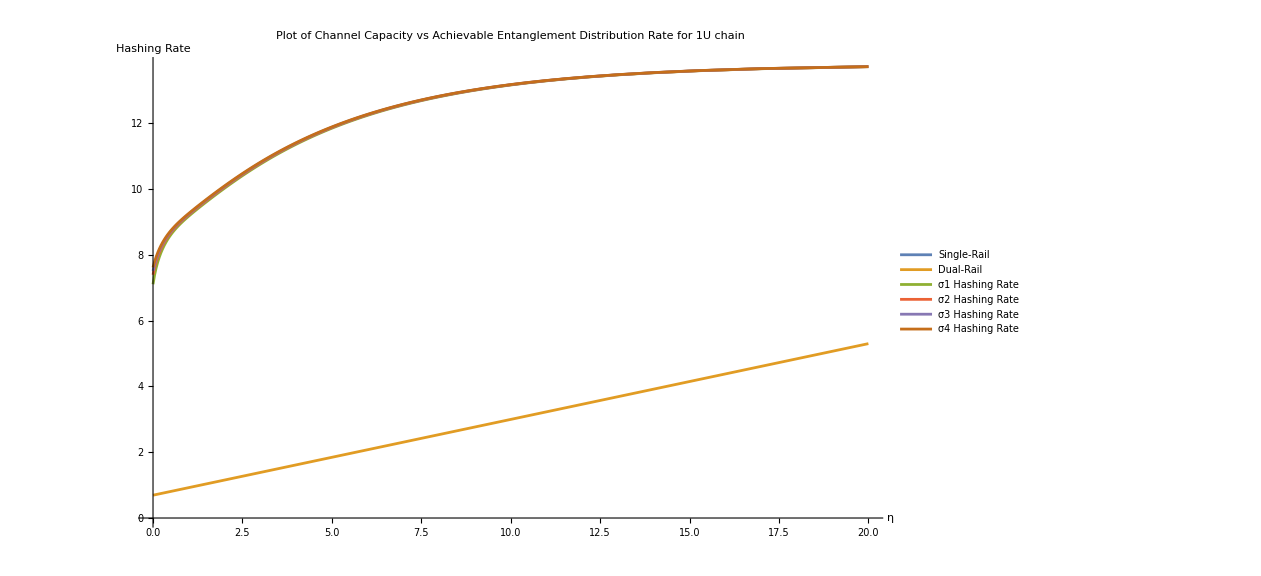

```mathematica
(*This plot shows the Rate Scaling of the Lossiest Link for the achievable entanglement distribution rate, where capacity upper bounds the rates, and so for GKP encoding we maximise over the post selection window to achieve the highest possible entanglement distribution rate*)
ListPlot[{SRhashingrate1 , DRhashingrate1tab ,hashingrateσ1η , hashingrateσ2η , hashingrateσ3η , hashingrateσ4η} , PlotRange->All , AxesStyle->Thick , Joined->True , AxesLabel->{Style["η",Directive[Black,16]], Style["Hashing Rate",Directive[Black,16]]} , PlotLabel-> Style["Plot of Channel Capacity vs Achievable Entanglement Distribution Rate for 1U chain" , Directive[Black , 20]] , PlotLegends->{Style["Single-Rail" , Directive[Black , 16]] , Style["Dual-Rail" , Directive[Black , 16]],Style["σ1 Hashing Rate" , Directive[Black , 16]],Style["σ2 Hashing Rate" , Directive[Black , 16]],Style["σ3 Hashing Rate" , Directive[Black , 16]],Style["σ4 Hashing Rate" , Directive[Black , 16]]} , TicksStyle->Directive["Label", 14]]
```

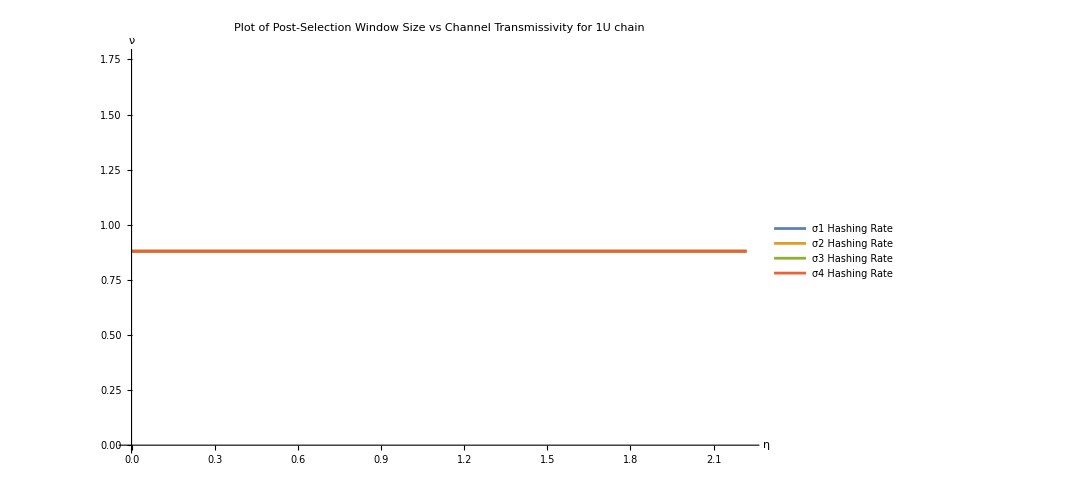

```mathematica
(*Investigating how size of post selection window changes as we vary channel transmissivity and the quality of the GKP qubits*)
ListPlot[{postselectiontableσ1 , postselectiontableσ2 , postselectiontableσ3 , postselectiontableσ4} , PlotRange->All , AxesStyle->Thick , Joined->True , AxesLabel->{Style["η",Directive[Black,16]], Style["ν",Directive[Black,16]]} , PlotLabel-> Style["Plot of Post-Selection Window Size vs Channel Transmissivity for 1U chain" , Directive[Black , 20]] , PlotLegends->{Style["σ1 Hashing Rate" , Directive[Black , 16]],Style["σ2 Hashing Rate" , Directive[Black , 16]],Style["σ3 Hashing Rate" , Directive[Black , 16]],Style["σ4 Hashing Rate" , Directive[Black , 16]]} , TicksStyle->Directive["Label", 14]]
```

```mathematica
(*We need to carry out the analysis for two chain link capacities and fidelities, the following code builds up a chain of 2 memory qubits using GKP states of varying width*)

chainfunction2[σ_ , ν_ , η_]:=rNtimes[newvector[σ , ν , η] , 2]

chain2σ1[ν_ , η_]:=chainfunction2[σ1 , ν , η]
chain2σ2[ν_ , η_]:=chainfunction2[σ2 , ν , η]
chain2σ3[ν_ , η_]:=chainfunction2[σ3 , ν , η]
chain2σ4[ν_ , η_]:=chainfunction2[σ4 , ν , η]

states2σ1[ν_ , η_]:= chain2σ1[ν , η][[1]] Φplus + chain2σ1[ν , η][[2]] Φminus + chain2σ1[ν , η][[3]] Ψplus + chain2σ1[ν , η][[4]] Ψminus
states2σ2[ν_ , η_]:= chain2σ2[ν , η][[1]] Φplus + chain2σ2[ν , η][[2]] Φminus + chain2σ2[ν , η][[3]] Ψplus + chain2σ2[ν , η][[4]] Ψminus
states2σ3[ν_ , η_]:= chain2σ3[ν , η][[1]] Φplus + chain2σ3[ν , η][[2]] Φminus + chain2σ3[ν , η][[3]] Ψplus + chain2σ3[ν , η][[4]] Ψminus
states2σ4[ν_ , η_]:= chain2σ4[ν , η][[1]] Φplus + chain2σ4[ν , η][[2]] Φminus + chain2σ4[ν , η][[3]] Ψplus + chain2σ4[ν , η][[4]] Ψminus

hashingrate2σ1[ν_ , η_] :=-Log[(Pc[σ1 , ν , η] + Pf[σ1 , ν , η])^4 * hashingbound[states2σ1[ν , η]]];
hashingrate2σ2[ν_ , η_] :=-Log[(Pc[σ2 , ν , η] + Pf[σ2 , ν , η])^4 * hashingbound[states2σ2[ν , η]]];
hashingrate2σ3[ν_ , η_] :=-Log[(Pc[σ3 , ν , η] + Pf[σ3 , ν , η])^4 * hashingbound[states2σ3[ν , η]]];
hashingrate2σ4[ν_ , η_] :=-Log[(Pc[σ4 , ν , η] + Pf[σ4 , ν , η])^4 * hashingbound[states2σ4[ν , η]]];

hashingrate2σ1TAB[η_] := Table[{ν , hashingrate2σ1[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate2σ2TAB[η_] := Table[{ν , hashingrate2σ2[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate2σ3TAB[η_] := Table[{ν , hashingrate2σ3[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate2σ4TAB[η_] := Table[{ν , hashingrate2σ4[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];

hashingrate2σ1η = Table[{-10*Log10[η] , MaximalBy[hashingrate2σ1TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrate2σ2η = Table[{-10*Log10[η] , MaximalBy[hashingrate2σ2TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrate2σ3η = Table[{-10*Log10[η] , MaximalBy[hashingrate2σ3TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrate2σ4η = Table[{-10*Log10[η] , MaximalBy[hashingrate2σ4TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];

postselectiontable2σ1 = Table[{-10*Log10[η] , MaximalBy[hashingrate2σ1TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
postselectiontable2σ2 = Table[{-10*Log10[η] , MaximalBy[hashingrate2σ2TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
postselectiontable2σ3 = Table[{-10*Log10[η] , MaximalBy[hashingrate2σ3TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
postselectiontable2σ4 = Table[{-10*Log10[η] , MaximalBy[hashingrate2σ4TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
```

```mathematica
(*Building SR and DR 2 link chains and finding their hashing rates*)

(*SR*)

(*Finding the hashing rate by multiplying the probability of success by the hashing bound*)
SRstate2[η_ , γ_] := dTraceSystem[KroneckerProduct[IdentityMatrix[2] , Φplus , IdentityMatrix[2]]. KroneckerProduct[QStateSingle[η , γ , 0 , 1] , QStateSingle[η , γ , 0 , 1]] . ConjugateTranspose[KroneckerProduct[IdentityMatrix[2] , Φplus , IdentityMatrix[2]]] / Tr[KroneckerProduct[IdentityMatrix[2] , Φplus , IdentityMatrix[2]]. KroneckerProduct[QStateSingle[η , γ , 0 , 1] , QStateSingle[η , γ , 0 , 1]] . ConjugateTranspose[KroneckerProduct[IdentityMatrix[2] , Φplus , IdentityMatrix[2]]]] , {2 , 3} , 2]
SRhashingrate2 = Table[{-10*Log10[η] , Max[Table[-Log[Tr[SingleRailState[η , γ , 0 , 1]]^2*hashingbound[SRstate2[η , γ]]] , {γ , 0 , 1 , 0.01}]]} , {η , 0 , 1 , 0.01}];

(*DR*)

DRtab2[η_] := rNtimes[QStateDual[η , 0 , 1]//Eigenvalues , 1];
DRstates2[η_] := DRtab2[η][[1]] * Φplus + DRtab2[η][[2]] * Φminus + DRtab2[η][[3]] * Ψplus + DRtab2[η][[4]] * Ψminus;
DRhashingrate2[η_] := -Log[Tr[DualRailState[η , 0 , 1]]^2 * hashingbound[DRstates2[η]]]
DRhashingrate2tab = Table[{-10*Log10[η] , DRhashingrate2[η]} , {η , 0.01 , 1 , 0.01}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Eigenvalues::mindet will be suppressed during this calculation.

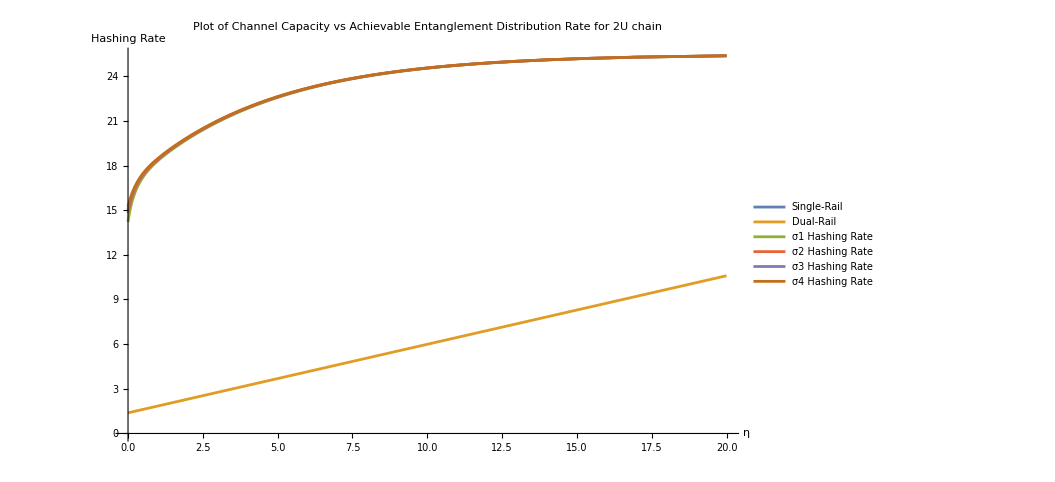

```mathematica
ListPlot[{SRhashingrate2 , DRhashingrate2tab ,hashingrate2σ1η , hashingrate2σ2η , hashingrate2σ3η , hashingrate2σ4η} , PlotRange->All , AxesStyle->Thick , Joined->True , AxesLabel->{Style["η",Directive[Black,16]], Style["Hashing Rate",Directive[Black,16]]} , PlotLabel-> Style["Plot of Channel Capacity vs Achievable Entanglement Distribution Rate for 2U chain" , Directive[Black , 20]] , PlotLegends->{Style["Single-Rail" , Directive[Black , 16]] , Style["Dual-Rail" , Directive[Black , 16]],Style["σ1 Hashing Rate" , Directive[Black , 16]],Style["σ2 Hashing Rate" , Directive[Black , 16]],Style["σ3 Hashing Rate" , Directive[Black , 16]],Style["σ4 Hashing Rate" , Directive[Black , 16]]} , TicksStyle->Directive["Label", 14]]
```

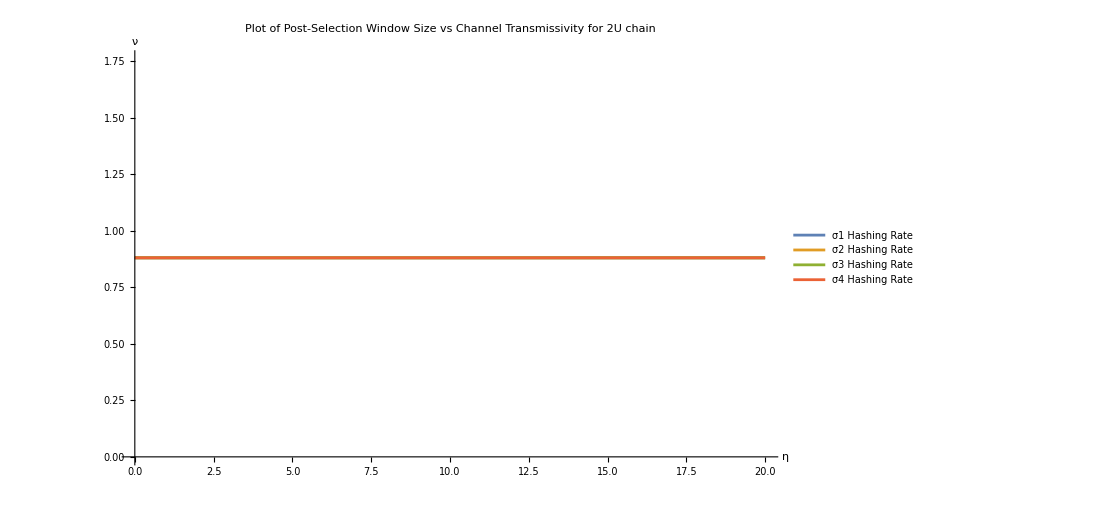

```mathematica
(*Investigating how size of post selection window changes as we vary channel transmissivity and the quality of the GKP qubits*)
ListPlot[{postselectiontable2σ1 , postselectiontable2σ2 , postselectiontable2σ3 , postselectiontable2σ4} , PlotRange->All , AxesStyle->Thick , Joined->True , AxesLabel->{Style["η",Directive[Black,16]], Style["ν",Directive[Black,16]]} , PlotLabel-> Style["Plot of Post-Selection Window Size vs Channel Transmissivity for 2U chain" , Directive[Black , 20]] , PlotLegends->{Style["σ1 Hashing Rate" , Directive[Black , 16]],Style["σ2 Hashing Rate" , Directive[Black , 16]],Style["σ3 Hashing Rate" , Directive[Black , 16]],Style["σ4 Hashing Rate" , Directive[Black , 16]]} , TicksStyle->Directive["Label", 14]]
```

```mathematica
(*We need to carry out the analysis for two chain link capacities and fidelities, the following code builds up a chain of 2 memory qubits using GKP states of varying width*)

chainfunction5[σ_ , ν_ , η_]:=rNtimes[newvector[σ , ν , η] , 5]

chain5σ1[ν_ , η_]:=chainfunction5[σ1 , ν , η]
chain5σ2[ν_ , η_]:=chainfunction5[σ2 , ν , η]
chain5σ3[ν_ , η_]:=chainfunction5[σ3 , ν , η]
chain5σ4[ν_ , η_]:=chainfunction5[σ4 , ν , η]

states5σ1[ν_ , η_]:= chain5σ1[ν , η][[1]] Φplus + chain5σ1[ν , η][[2]] Φminus + chain5σ1[ν , η][[3]] Ψplus + chain5σ1[ν , η][[4]] Ψminus
states5σ2[ν_ , η_]:= chain5σ2[ν , η][[1]] Φplus + chain5σ2[ν , η][[2]] Φminus + chain5σ2[ν , η][[3]] Ψplus + chain5σ2[ν , η][[4]] Ψminus
states5σ3[ν_ , η_]:= chain5σ3[ν , η][[1]] Φplus + chain5σ3[ν , η][[2]] Φminus + chain5σ3[ν , η][[3]] Ψplus + chain5σ3[ν , η][[4]] Ψminus
states5σ4[ν_ , η_]:= chain5σ4[ν , η][[1]] Φplus + chain5σ4[ν , η][[2]] Φminus + chain5σ4[ν , η][[3]] Ψplus + chain5σ4[ν , η][[4]] Ψminus

hashingrate5σ1[ν_ , η_] :=-Log[(Pc[σ1 , ν , η] + Pf[σ1 , ν , η])^10 * hashingbound[states5σ1[ν , η]]];
hashingrate5σ2[ν_ , η_] :=-Log[(Pc[σ2 , ν , η] + Pf[σ2 , ν , η])^10 * hashingbound[states5σ2[ν , η]]];
hashingrate5σ3[ν_ , η_] :=-Log[(Pc[σ3 , ν , η] + Pf[σ3 , ν , η])^10 * hashingbound[states5σ3[ν , η]]];
hashingrate5σ4[ν_ , η_] :=-Log[(Pc[σ4 , ν , η] + Pf[σ4 , ν , η])^10 * hashingbound[states5σ4[ν , η]]];

hashingrate5σ1TAB[η_] := Table[{ν , hashingrate5σ1[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate5σ2TAB[η_] := Table[{ν , hashingrate5σ2[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate5σ3TAB[η_] := Table[{ν , hashingrate5σ3[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate5σ4TAB[η_] := Table[{ν , hashingrate5σ4[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];

hashingrate5σ1η = Table[{-10*Log10[η] , MaximalBy[hashingrate5σ1TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrate5σ2η = Table[{-10*Log10[η] , MaximalBy[hashingrate5σ2TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrate5σ3η = Table[{-10*Log10[η] , MaximalBy[hashingrate5σ3TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrate5σ4η = Table[{-10*Log10[η] , MaximalBy[hashingrate5σ4TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];

postselectiontable5σ1 = Table[{-10*Log10[η] , MaximalBy[hashingrate5σ1TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
postselectiontable5σ2 = Table[{-10*Log10[η] , MaximalBy[hashingrate5σ2TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
postselectiontable5σ3 = Table[{-10*Log10[η] , MaximalBy[hashingrate5σ3TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
postselectiontable5σ4 = Table[{-10*Log10[η] , MaximalBy[hashingrate5σ4TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
```

```mathematica
(*SR*)


(*Finding the hashing rate by multiplying the probability of success by the hashing bound*)

(*We can no longer use the SRstate50CORRECT code as this takes too long*)
BSM = KroneckerProduct[IdentityMatrix[2] , Φplus , IdentityMatrix[2]];

(*Start with 2U block*)
Qinit[η_,γ_]:=QStateSingle[η,γ,0,1];

(*Initialize chain with two blocks and one BSM*)initialState[η_,γ_]:=Module[{ρ2},ρ2=KroneckerProduct[Qinit[η,γ],Qinit[η,γ]];
ρ2=BSM.ρ2.ConjugateTranspose[BSM];
ρ2/Tr[ρ2]//dTraceSystem[#,{2,3},2]&];

(*Add another 2U block with BSM between qubits 2 and 3*)
extendState[ρ_,η_,γ_]:=Module[{ρext},ρext=KroneckerProduct[ρ,Qinit[η,γ]];
ρext=BSM.ρext.ConjugateTranspose[BSM];
ρext/Tr[ρext]//dTraceSystem[#,{2,3},2]&];

(*Build the full 50-unit chain*)
chainState5[η_,γ_]:=Module[{ρ,i},ρ=initialState[η,γ];
For[i=1,i<=3,i++,(*Already used 1 BSM above*)ρ=extendState[ρ,η,γ];];
ρ];
SRhasingrate5 = Table[{-10*Log10[η] , Max[Table[-Log[Tr[SingleRailState[η , γ , 0 , 1]]^5*hashingbound[chainState5[η , γ]]] , {γ , 0 , 1 , 0.01}]]} , {η , 0 , 1 , 0.01}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Eigenvalues::mindet will be suppressed during this calculation.

Max::nord: Invalid comparison with {Indeterminate,Indeterminate,46.3815-3.14159 ⅈ,Indeterminate,42.9087,40.9752,39.3089,37.8889,36.6549,35.5629,34.5832,33.6943,32.8807,32.1302,«23»,22.2742,22.0339,21.8019,21.5781,21.3621,21.1539,20.9532,20.76,20.574,20.3952,20.2235,20.0589,19.9011,«51»} attempted.

Max::nord: Invalid comparison with {Indeterminate,44.4145-3.14159 ⅈ,42.9508-3.14159 ⅈ,42.8863,39.8927,37.8808,36.2021,34.7783,33.5412,32.4464,31.4639,30.5725,29.7564,«25»,18.9208,18.6927,18.4728,18.2612,18.0574,17.8615,17.6732,17.4925,17.3191,17.153,16.9941,16.8424,«51»} attempted.

Max::nord: Invalid comparison with {Indeterminate,42.9066-3.14159 ⅈ,43.8576-3.14159 ⅈ,40.1551,37.8282,35.7646,34.0807,32.6541,31.4135,30.3155,29.33,28.4357,27.6171,«25»,16.8046,16.5811,16.3662,16.1597,15.9614,15.7712,15.5888,15.4141,15.247,15.0874,14.9351,14.7902,«51»} attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

```mathematica
(*DR*)

DRtab5[η_] := rNtimes[QStateDual[η , 0 , 1]//Eigenvalues , 4];
DRstate5[η_] := DRtab5[η][[1]] * Φplus + DRtab5[η][[2]] * Φminus + DRtab5[η][[3]] * Ψplus + DRtab5[η][[4]] * Ψminus;
DRhashingrate5[η_] := -Log[Tr[DualRailState[η , 0 , 1]]^5 * hashingbound[DRstate5[η]]]
DRhashingrate5tab = Table[{-10*Log10[η] , DRhashingrate5[η]} , {η , 0.01 , 1 , 0.01}];
```

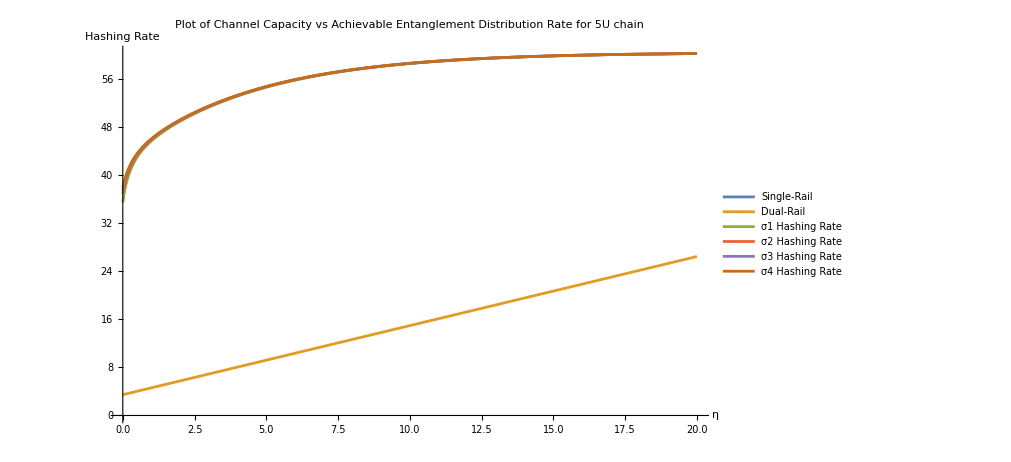

```mathematica
ListPlot[{SRhasingrate5 , DRhashingrate5tab ,hashingrate5σ1η , hashingrate5σ2η , hashingrate5σ3η , hashingrate5σ4η} , PlotRange->All , AxesStyle->Thick , Joined->True ,AxesLabel->{Style["η",Directive[Black,16]], Style["Hashing Rate",Directive[Black,16]]} , PlotLabel-> Style["Plot of Channel Capacity vs Achievable Entanglement Distribution Rate for 5U chain" , Directive[Black , 20]] , PlotLegends->{Style["Single-Rail" , Directive[Black , 16]] , Style["Dual-Rail" , Directive[Black , 16]],Style["σ1 Hashing Rate" , Directive[Black , 16]],Style["σ2 Hashing Rate" , Directive[Black , 16]],Style["σ3 Hashing Rate" , Directive[Black , 16]],Style["σ4 Hashing Rate" , Directive[Black , 16]]} , TicksStyle->Directive["Label", 14]]
```

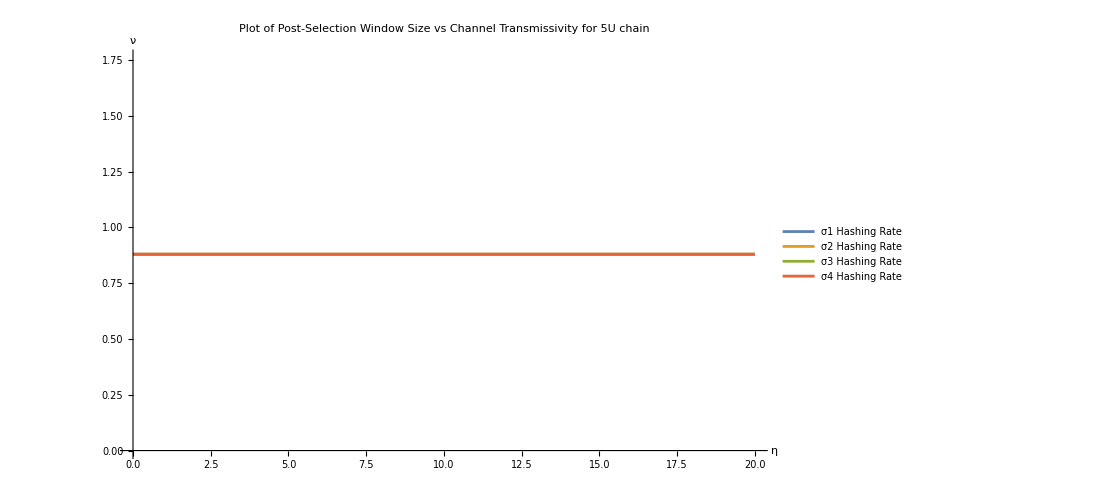

```mathematica
(*Investigating how size of post selection window changes as we vary channel transmissivity and the quality of the GKP qubits*)
ListPlot[{postselectiontable5σ1 , postselectiontable5σ2 , postselectiontable5σ3 , postselectiontable5σ4} , PlotRange->All , AxesStyle->Thick , Joined->True , AxesLabel->{Style["η",Directive[Black,16]], Style["ν",Directive[Black,16]]} , PlotLabel-> Style["Plot of Post-Selection Window Size vs Channel Transmissivity for 5U chain" , Directive[Black , 20]] , PlotLegends->{Style["σ1 Hashing Rate" , Directive[Black , 16]],Style["σ2 Hashing Rate" , Directive[Black , 16]],Style["σ3 Hashing Rate" , Directive[Black , 16]],Style["σ4 Hashing Rate" , Directive[Black , 16]]} , TicksStyle->Directive["Label", 14]]
```

```mathematica
(*We need to carry out the analysis for two chain link capacities and fidelities, the following code builds up a chain of 50 memory qubits using GKP states of varying width*)

chainfunction10[σ_ , ν_ , η_]:=rNtimes[newvector[σ , ν , η] , 10]

chain10σ1[ν_ , η_]:=chainfunction100[σ1 , ν , η]
chain10σ2[ν_ , η_]:=chainfunction100[σ2 , ν , η]
chain10σ3[ν_ , η_]:=chainfunction100[σ3 , ν , η]
chain10σ4[ν_ , η_]:=chainfunction100[σ4 , ν , η]

states10σ1[ν_ , η_]:= chain10σ1[ν , η][[1]] Φplus + chain10σ1[ν , η][[2]] Φminus + chain10σ1[ν , η][[3]] Ψplus + chain10σ1[ν , η][[4]] Ψminus
states10σ2[ν_ , η_]:= chain10σ2[ν , η][[1]] Φplus + chain10σ2[ν , η][[2]] Φminus + chain10σ2[ν , η][[3]] Ψplus + chain10σ2[ν , η][[4]] Ψminus
states10σ3[ν_ , η_]:= chain10σ3[ν , η][[1]] Φplus + chain10σ3[ν , η][[2]] Φminus + chain10σ3[ν , η][[3]] Ψplus + chain10σ3[ν , η][[4]] Ψminus
states10σ4[ν_ , η_]:= chain10σ4[ν , η][[1]] Φplus + chain10σ4[ν , η][[2]] Φminus + chain10σ4[ν , η][[3]] Ψplus + chain10σ4[ν , η][[4]] Ψminus

hashingrate10σ1[ν_ , η_] :=-Log[(Pc[σ1 , ν , η] + Pf[σ1 , ν , η])^20 * hashingbound[states10σ1[ν , η]]];
hashingrate10σ2[ν_ , η_] :=-Log[(Pc[σ2 , ν , η] + Pf[σ2 , ν , η])^20 * hashingbound[states10σ2[ν , η]]];
hashingrate10σ3[ν_ , η_] :=-Log[(Pc[σ3 , ν , η] + Pf[σ3 , ν , η])^20 * hashingbound[states10σ3[ν , η]]];
hashingrate10σ4[ν_ , η_] :=-Log[(Pc[σ4 , ν , η] + Pf[σ4 , ν , η])^20 * hashingbound[states10σ4[ν , η]]];

hashingrate10σ1TAB[η_] := Table[{ν , hashingrate10σ1[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate10σ2TAB[η_] := Table[{ν , hashingrate10σ2[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate10σ3TAB[η_] := Table[{ν , hashingrate10σ3[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate10σ4TAB[η_] := Table[{ν , hashingrate10σ4[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];

hashingrate10σ1η = Table[{-10*Log10[η] , MaximalBy[hashingrate10σ1TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrate10σ2η = Table[{-10*Log10[η] , MaximalBy[hashingrate10σ2TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrate10σ3η = Table[{-10*Log10[η] , MaximalBy[hashingrate10σ3TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrate10σ4η = Table[{-10*Log10[η] , MaximalBy[hashingrate10σ4TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];

postselectiontable10σ1 = Table[{-10*Log10[η] , MaximalBy[hashingrate10σ1TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
postselectiontable10σ2 = Table[{-10*Log10[η] , MaximalBy[hashingrate10σ2TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
postselectiontable10σ3 = Table[{-10*Log10[η] , MaximalBy[hashingrate10σ3TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
postselectiontable10σ4 = Table[{-10*Log10[η] , MaximalBy[hashingrate10σ4TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
```

Part::partw: Part 4 of chainfunction100[0.173205,0.,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.173205,0.01,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.173205,0.02,0.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of chainfunction100[0.2,0.,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.2,0.01,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.2,0.02,0.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of chainfunction100[0.212132,0.,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.212132,0.01,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.212132,0.02,0.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of chainfunction100[0.223607,0.,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.223607,0.01,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.223607,0.02,0.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of chainfunction100[0.173205,0.,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.173205,0.01,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.173205,0.02,0.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of chainfunction100[0.2,0.,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.2,0.01,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.2,0.02,0.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of chainfunction100[0.212132,0.,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.212132,0.01,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.212132,0.02,0.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of chainfunction100[0.223607,0.,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.223607,0.01,0.] does not exist.

Part::partw: Part 4 of chainfunction100[0.223607,0.02,0.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*Building SR and DR 2 link chains and finding their hashing rates*)

(*SR*)


(*Finding the hashing rate by multiplying the probability of success by the hashing bound*)

(*We can no longer use the SRstate50CORRECT code as this takes too long*)
BSM = KroneckerProduct[IdentityMatrix[2] , Φplus , IdentityMatrix[2]];

(*Start with 2U block*)
Qinit[η_,γ_]:=QStateSingle[η,γ,0,1];

(*Initialize chain with two blocks and one BSM*)initialState[η_,γ_]:=Module[{ρ2},ρ2=KroneckerProduct[Qinit[η,γ],Qinit[η,γ]];
ρ2=BSM.ρ2.ConjugateTranspose[BSM];
ρ2/Tr[ρ2]//dTraceSystem[#,{2,3},2]&];

(*Add another 2U block with BSM between qubits 2 and 3*)
extendState[ρ_,η_,γ_]:=Module[{ρext},ρext=KroneckerProduct[ρ,Qinit[η,γ]];
ρext=BSM.ρext.ConjugateTranspose[BSM];
ρext/Tr[ρext]//dTraceSystem[#,{2,3},2]&];

(*Build the full 50-unit chain*)
chainState10[η_,γ_]:=Module[{ρ,i},ρ=initialState[η,γ];
For[i=1,i<=8,i++,(*Already used 1 BSM above*)ρ=extendState[ρ,η,γ];];
ρ];
SRhasingrate10 = Table[{-10*Log10[η] , Max[Table[-Log[Tr[SingleRailState[η , γ , 0 , 1]]^10*hashingbound[chainState10[η , γ]]] , {γ , 0 , 1 , 0.01}]]} , {η , 0 , 1 , 0.01}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Eigenvalues::mindet will be suppressed during this calculation.

Max::nord: Invalid comparison with {Indeterminate,56.7468,55.0454,Indeterminate,54.2487,53.9369,54.4371,55.9193-3.14159 ⅈ,55.3233-3.14159 ⅈ,55.4215,55.521,54.9286,55.0307,Indeterminate,«24»,44.7836,44.2686,43.7716,43.2922,42.83,42.3846,41.9557,41.543,41.1464,40.7655,40.4001,40.0502,«51»} attempted.

Max::nord: Invalid comparison with {Indeterminate,51.8009,52.0402,51.1455-3.14159 ⅈ,Indeterminate,52.7074-3.14159 ⅈ,51.6983-3.14159 ⅈ,Indeterminate,51.5931-3.14159 ⅈ,51.2807,Indeterminate,Indeterminate,52.666,«26»,40.3426,39.8515,39.3783,38.9226,38.484,38.0622,37.6569,37.2678,36.8947,36.5374,36.1957,«51»} attempted.

Max::nord: Invalid comparison with {Indeterminate,50.0128,50.3812-3.14159 ⅈ,49.2589,50.9512,50.342-3.14159 ⅈ,51.1202-3.14159 ⅈ,50.5134,50.6009-3.14159 ⅈ,Indeterminate,50.7795-3.14159 ⅈ,49.4845,«28»,37.4655,36.9976,36.5474,36.1145,35.6986,35.2994,34.9166,34.55,34.1993,33.8643,«51»} attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

```mathematica
(*DR*)

DRtab10[η_] := rNtimes[QStateDual[η , 0 , 1]//Eigenvalues , 9];
DRstates10[η_] := DRtab10[η][[1]] * Φplus + DRtab10[η][[2]] * Φminus + DRtab10[η][[3]] * Ψplus + DRtab10[η][[4]] * Ψminus;
DRhashingrate10[η_] := -Log[Tr[DualRailState[η , 0 , 1]]^10 * hashingbound[DRstates10[η]]]
DRhashingrate10tab = Table[{-10*Log10[η] , DRhashingrate10[η]} , {η , 0.01 , 1 , 0.01}];
```

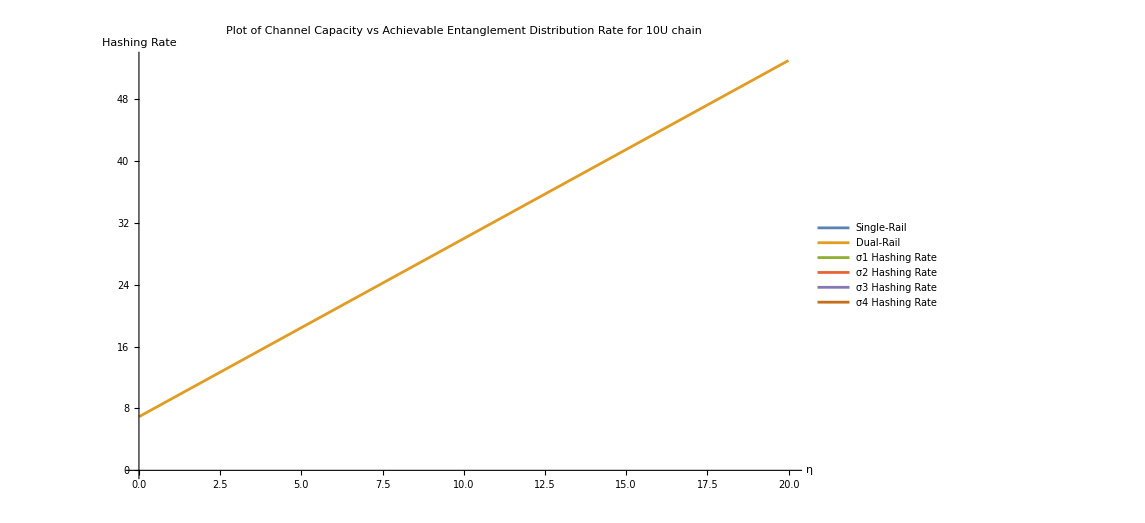

```mathematica
ListPlot[{SRhasingrate10 , DRhashingrate10tab ,hashingrate10σ1η , hashingrate10σ2η , hashingrate10σ3η , hashingrate10σ4η} , PlotRange->All , AxesStyle->Thick , Joined->True ,AxesLabel->{Style["η",Directive[Black,16]], Style["Hashing Rate",Directive[Black,16]]} , PlotLabel-> Style["Plot of Channel Capacity vs Achievable Entanglement Distribution Rate for 10U chain" , Directive[Black , 20]] , PlotLegends->{Style["Single-Rail" , Directive[Black , 16]] , Style["Dual-Rail" , Directive[Black , 16]],Style["σ1 Hashing Rate" , Directive[Black , 16]],Style["σ2 Hashing Rate" , Directive[Black , 16]],Style["σ3 Hashing Rate" , Directive[Black , 16]],Style["σ4 Hashing Rate" , Directive[Black , 16]]} , TicksStyle->Directive["Label", 14]]
```

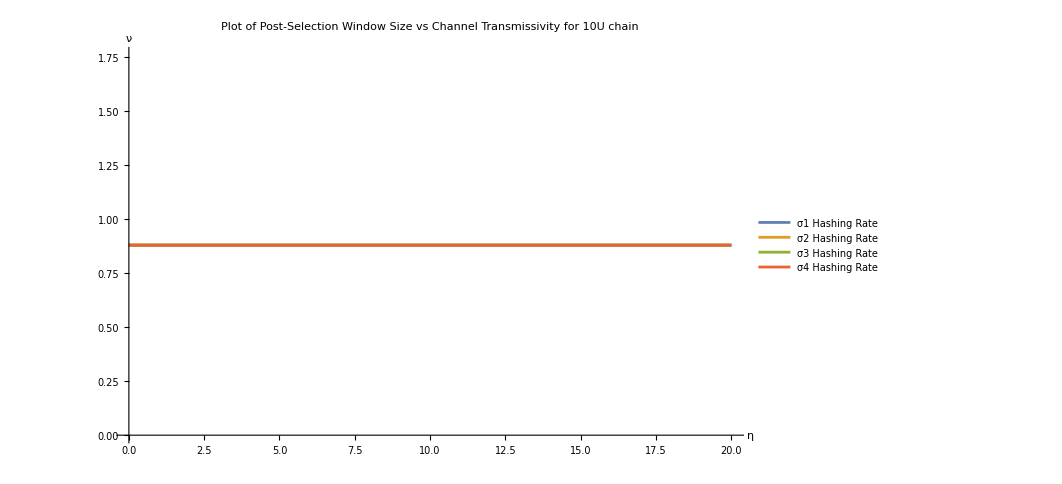

```mathematica
(*Investigating how size of post selection window changes as we vary channel transmissivity and the quality of the GKP qubits*)
ListPlot[{postselectiontable10σ1 , postselectiontable10σ2 , postselectiontable10σ3 , postselectiontable10σ4} , PlotRange->All , AxesStyle->Thick , Joined->True , AxesLabel->{Style["η",Directive[Black,16]], Style["ν",Directive[Black,16]]} , PlotLabel-> Style["Plot of Post-Selection Window Size vs Channel Transmissivity for 10U chain" , Directive[Black , 20]] , PlotLegends->{Style["σ1 Hashing Rate" , Directive[Black , 16]],Style["σ2 Hashing Rate" , Directive[Black , 16]],Style["σ3 Hashing Rate" , Directive[Black , 16]],Style["σ4 Hashing Rate" , Directive[Black , 16]]} , TicksStyle->Directive["Label", 14]]
```

```mathematica
(*We need to carry out the analysis for two chain link capacities and fidelities, the following code builds up a chain of 50 memory qubits using GKP states of varying width*)

chainfunction50[σ_ , ν_ , η_]:=rNtimes[newvector[σ , ν , η] , 50]

chain50σ1[ν_ , η_]:=chainfunction50[σ1 , ν , η]
chain50σ2[ν_ , η_]:=chainfunction50[σ2 , ν , η]
chain50σ3[ν_ , η_]:=chainfunction50[σ3 , ν , η]
chain50σ4[ν_ , η_]:=chainfunction50[σ4 , ν , η]

states50σ1[ν_ , η_]:= chain50σ1[ν , η][[1]] Φplus + chain50σ1[ν , η][[2]] Φminus + chain50σ1[ν , η][[3]] Ψplus + chain50σ1[ν , η][[4]] Ψminus
states50σ2[ν_ , η_]:= chain50σ2[ν , η][[1]] Φplus + chain50σ2[ν , η][[2]] Φminus + chain50σ2[ν , η][[3]] Ψplus + chain50σ2[ν , η][[4]] Ψminus
states50σ3[ν_ , η_]:= chain50σ3[ν , η][[1]] Φplus + chain50σ3[ν , η][[2]] Φminus + chain50σ3[ν , η][[3]] Ψplus + chain50σ3[ν , η][[4]] Ψminus
states50σ4[ν_ , η_]:= chain50σ4[ν , η][[1]] Φplus + chain50σ4[ν , η][[2]] Φminus + chain50σ4[ν , η][[3]] Ψplus + chain50σ4[ν , η][[4]] Ψminus

hashingrate50σ1[ν_ , η_] :=-Log[(Pc[σ1 , ν , η] + Pf[σ1 , ν , η])^100 * hashingbound[states50σ1[ν , η]]];
hashingrate50σ2[ν_ , η_] :=-Log[(Pc[σ2 , ν , η] + Pf[σ2 , ν , η])^100 * hashingbound[states50σ2[ν , η]]];
hashingrate50σ3[ν_ , η_] :=-Log[(Pc[σ3 , ν , η] + Pf[σ3 , ν , η])^100 * hashingbound[states50σ3[ν , η]]];
hashingrate50σ4[ν_ , η_] :=-Log[(Pc[σ4 , ν , η] + Pf[σ4 , ν , η])^100 * hashingbound[states50σ4[ν , η]]];

hashingrate50σ1TAB[η_] := Table[{ν , hashingrate50σ1[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate50σ2TAB[η_] := Table[{ν , hashingrate50σ2[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate50σ3TAB[η_] := Table[{ν , hashingrate50σ3[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate50σ4TAB[η_] := Table[{ν , hashingrate50σ4[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];

hashingrate50σ1η = Table[{-10*Log10[η] , MaximalBy[hashingrate50σ1TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrate50σ2η = Table[{-10*Log10[η] , MaximalBy[hashingrate50σ2TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrate50σ3η = Table[{-10*Log10[η] , MaximalBy[hashingrate50σ3TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrate50σ4η = Table[{-10*Log10[η] , MaximalBy[hashingrate50σ4TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];

postselectiontable50σ1 = Table[{-10*Log10[η] , MaximalBy[hashingrate50σ1TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
postselectiontable50σ2 = Table[{-10*Log10[η] , MaximalBy[hashingrate50σ2TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
postselectiontable50σ3 = Table[{-10*Log10[η] , MaximalBy[hashingrate50σ3TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
postselectiontable50σ4 = Table[{-10*Log10[η] , MaximalBy[hashingrate50σ4TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
```

```mathematica
(*SR*)


(*Finding the hashing rate by multiplying the probability of success by the hashing bound*)

(*We can no longer use the SRstate50CORRECT code as this takes too long*)
BSM = KroneckerProduct[IdentityMatrix[2] , Φplus , IdentityMatrix[2]];

(*Start with 2U block*)
Qinit[η_,γ_]:=QStateSingle[η,γ,0,1];

(*Initialize chain with two blocks and one BSM*)initialState[η_,γ_]:=Module[{ρ2},ρ2=KroneckerProduct[Qinit[η,γ],Qinit[η,γ]];
ρ2=BSM.ρ2.ConjugateTranspose[BSM];
ρ2/Tr[ρ2]//dTraceSystem[#,{2,3},2]&];

(*Add another 2U block with BSM between qubits 2 and 3*)
extendState[ρ_,η_,γ_]:=Module[{ρext},ρext=KroneckerProduct[ρ,Qinit[η,γ]];
ρext=BSM.ρext.ConjugateTranspose[BSM];
ρext/Tr[ρext]//dTraceSystem[#,{2,3},2]&];

(*Build the full 50-unit chain*)
chainState[η_,γ_]:=Module[{ρ,i},ρ=initialState[η,γ];
For[i=1,i<=48,i++,(*Already used 1 BSM above*)ρ=extendState[ρ,η,γ];];
ρ];
SRhasingrate50 = Table[{-10*Log10[η] , Max[Table[-Log[Tr[SingleRailState[η , γ , 0 , 1]]^50*hashingbound[chainState[η , γ]]] , {γ , 0 , 1 , 0.01}]]} , {η , 0 , 1 , 0.01}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Eigenvalues::mindet will be suppressed during this calculation.

Max::nord: Invalid comparison with {Indeterminate,124.087,123.258,124.814,124.296,124.541,124.545,127.104-3.14159 ⅈ,126.896-3.14159 ⅈ,Indeterminate,127.885,127.696,128.206,Indeterminate,«24»,Indeterminate,145.071,145.844,146.631-3.14159 ⅈ,Indeterminate,148.249,Indeterminate,149.929,Indeterminate,151.675,Indeterminate,Indeterminate,«51»} attempted.

Max::nord: Invalid comparison with {Indeterminate,108.751,108.35,108.78-3.14159 ⅈ,Indeterminate,110.352-3.14159 ⅈ,110.394-3.14159 ⅈ,Indeterminate,111.018-3.14159 ⅈ,111.484,Indeterminate,«29»,129.855-3.14159 ⅈ,Indeterminate,131.396,Indeterminate,Indeterminate,133.821,Indeterminate,134.826-3.14159 ⅈ,136.396-3.14159 ⅈ,137.29,«51»} attempted.

Max::nord: Invalid comparison with {Indeterminate,99.7157,101.035-3.14159 ⅈ,100.24,102.263,101.99,102.416-3.14159 ⅈ,100.139,103.285-3.14159 ⅈ,Indeterminate,104.178,103.535,«27»,119.348-3.14159 ⅈ,Indeterminate,121.515,122.273-3.14159 ⅈ,123.047,123.143,124.641,Indeterminate,125.609,Indeterminate,Indeterminate,«51»} attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

```mathematica
(*DR*)

DRtab50[η_] := rNtimes[QStateDual[η , 0 , 1]//Eigenvalues , 49];
DRstates50[η_] := DRtab50[η][[1]] * Φplus + DRtab50[η][[2]] * Φminus + DRtab50[η][[3]] * Ψplus + DRtab50[η][[4]] * Ψminus;
DRhashingrate50[η_] := -Log[Tr[DualRailState[η , 0 , 1]]^50 * hashingbound[DRstates50[η]]]
DRhashingrate50tab = Table[{-10*Log10[η] , DRhashingrate50[η]} , {η , 0.01 , 1 , 0.01}];
```

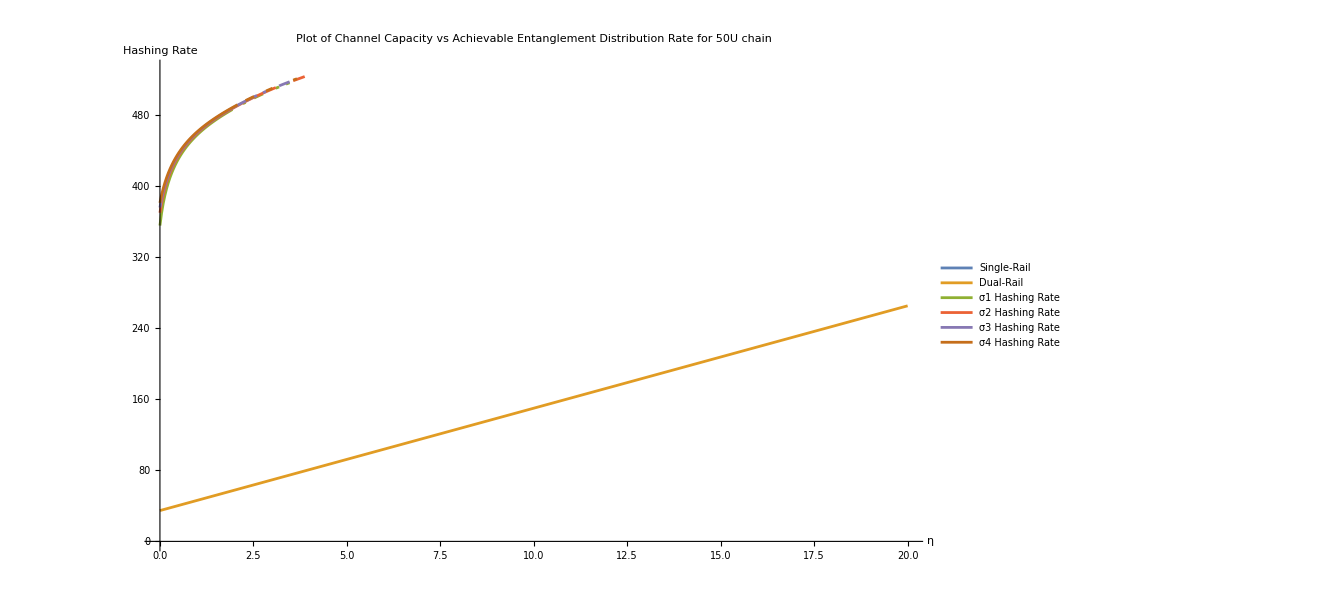

```mathematica
ListPlot[{SRhasingrate50 , DRhashingrate50tab ,hashingrate50σ1η , hashingrate50σ2η , hashingrate50σ3η , hashingrate50σ4η} , PlotRange->All , AxesStyle->Thick , Joined->True ,AxesLabel->{Style["η",Directive[Black,16]], Style["Hashing Rate",Directive[Black,16]]} , PlotLabel-> Style["Plot of Channel Capacity vs Achievable Entanglement Distribution Rate for 50U chain" , Directive[Black , 20]] , PlotLegends->{Style["Single-Rail" , Directive[Black , 16]] , Style["Dual-Rail" , Directive[Black , 16]],Style["σ1 Hashing Rate" , Directive[Black , 16]],Style["σ2 Hashing Rate" , Directive[Black , 16]],Style["σ3 Hashing Rate" , Directive[Black , 16]],Style["σ4 Hashing Rate" , Directive[Black , 16]]} , TicksStyle->Directive["Label", 14]]
```

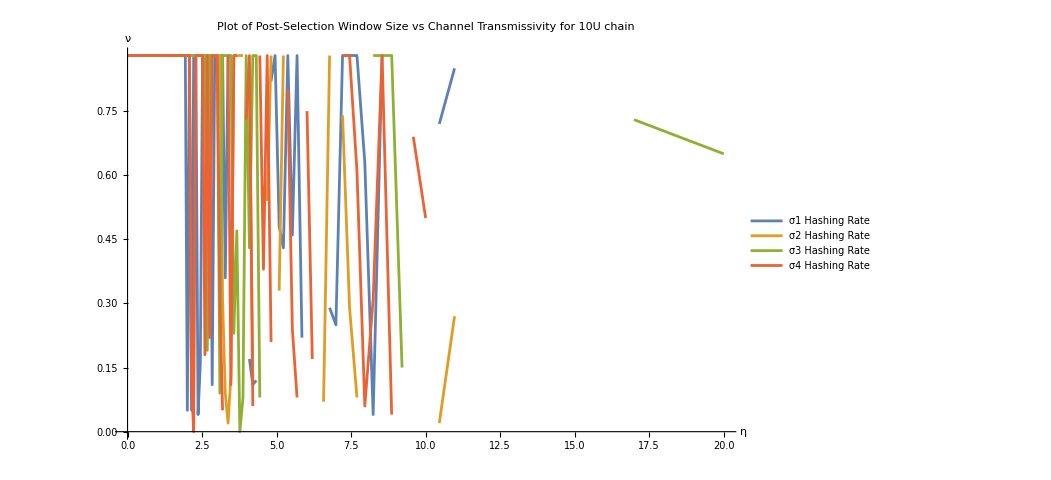

```mathematica
(*Investigating how size of post selection window changes as we vary channel transmissivity and the quality of the GKP qubits*)
ListPlot[{postselectiontable50σ1 , postselectiontable50σ2 , postselectiontable50σ3 , postselectiontable50σ4} , PlotRange->All , AxesStyle->Thick , Joined->True , AxesLabel->{Style["η",Directive[Black,16]], Style["ν",Directive[Black,16]]} , PlotLabel-> Style["Plot of Post-Selection Window Size vs Channel Transmissivity for 10U chain" , Directive[Black , 20]] , PlotLegends->{Style["σ1 Hashing Rate" , Directive[Black , 16]],Style["σ2 Hashing Rate" , Directive[Black , 16]],Style["σ3 Hashing Rate" , Directive[Black , 16]],Style["σ4 Hashing Rate" , Directive[Black , 16]]} , TicksStyle->Directive["Label", 14]]
```

```mathematica
(*We need to carry out the analysis for two chain link capacities and fidelities, the following code builds up a chain of 50 memory qubits using GKP states of varying width*)

chainfunction100[σ_ , ν_ , η_]:=rNtimes[newvector[σ , ν , η] , 100]

chain100σ1[ν_ , η_]:=chainfunction100[σ1 , ν , η]
chain100σ2[ν_ , η_]:=chainfunction100[σ2 , ν , η]
chain100σ3[ν_ , η_]:=chainfunction100[σ3 , ν , η]
chain100σ4[ν_ , η_]:=chainfunction100[σ4 , ν , η]

states100σ1[ν_ , η_]:= chain100σ1[ν , η][[1]] Φplus + chain100σ1[ν , η][[2]] Φminus + chain100σ1[ν , η][[3]] Ψplus + chain100σ1[ν , η][[4]] Ψminus
states100σ2[ν_ , η_]:= chain100σ2[ν , η][[1]] Φplus + chain100σ2[ν , η][[2]] Φminus + chain100σ2[ν , η][[3]] Ψplus + chain100σ2[ν , η][[4]] Ψminus
states100σ3[ν_ , η_]:= chain100σ3[ν , η][[1]] Φplus + chain100σ3[ν , η][[2]] Φminus + chain100σ3[ν , η][[3]] Ψplus + chain100σ3[ν , η][[4]] Ψminus
states100σ4[ν_ , η_]:= chain100σ4[ν , η][[1]] Φplus + chain100σ4[ν , η][[2]] Φminus + chain100σ4[ν , η][[3]] Ψplus + chain100σ4[ν , η][[4]] Ψminus

hashingrate100σ1[ν_ , η_] :=-Log[(Pc[σ1 , ν , η] + Pf[σ1 , ν , η])^200 * hashingbound[states100σ1[ν , η]]];
hashingrate100σ2[ν_ , η_] :=-Log[(Pc[σ2 , ν , η] + Pf[σ2 , ν , η])^200 * hashingbound[states100σ2[ν , η]]];
hashingrate100σ3[ν_ , η_] :=-Log[(Pc[σ3 , ν , η] + Pf[σ3 , ν , η])^200 * hashingbound[states100σ3[ν , η]]];
hashingrate100σ4[ν_ , η_] :=-Log[(Pc[σ4 , ν , η] + Pf[σ4 , ν , η])^200 * hashingbound[states100σ4[ν , η]]];

hashingrate100σ1TAB[η_] := Table[{ν , hashingrate100σ1[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate100σ2TAB[η_] := Table[{ν , hashingrate100σ2[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate100σ3TAB[η_] := Table[{ν , hashingrate100σ3[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
hashingrate100σ4TAB[η_] := Table[{ν , hashingrate100σ4[ν , η]} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];

hashingrate100σ1η = Table[{-10*Log10[η] , MaximalBy[hashingrate100σ1TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrate100σ2η = Table[{-10*Log10[η] , MaximalBy[hashingrate100σ2TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrate100σ3η = Table[{-10*Log10[η] , MaximalBy[hashingrate100σ3TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];
hashingrate100σ4η = Table[{-10*Log10[η] , MaximalBy[hashingrate100σ4TAB[η] , Last]/.{{x_ , y_}} -> y} , {η , 0 , 1 , 0.01}];

postselectiontable100σ1 = Table[{-10*Log10[η] , MaximalBy[hashingrate100σ1TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
postselectiontable100σ2 = Table[{-10*Log10[η] , MaximalBy[hashingrate100σ2TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
postselectiontable100σ3 = Table[{-10*Log10[η] , MaximalBy[hashingrate100σ3TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
postselectiontable100σ4 = Table[{-10*Log10[η] , MaximalBy[hashingrate100σ4TAB[η] , Last]/.{{x_ , y_}} -> x} , {η , 0 , 1 , 0.01}];
```

General::munfl: 2.16069×10^-306 (-1.33227×10^-15) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0183301^200 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00703401^200 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 2.16069×10^-306 (-1.33227×10^-15) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0183301^200 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00703401^200 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 2.16069×10^-306 (-1.33227×10^-15) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0183301^200 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00703401^200 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 2.16069×10^-306 (-1.33227×10^-15) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0183301^200 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00703401^200 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 2.16069×10^-306 (-1.33227×10^-15) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0183301^200 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00703401^200 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 2.16069×10^-306 (-1.33227×10^-15) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0183301^200 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00703401^200 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 2.16069×10^-306 (-1.33227×10^-15) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0183301^200 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00703401^200 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 2.16069×10^-306 (-1.33227×10^-15) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0183301^200 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00703401^200 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
(*SR*)


(*Finding the hashing rate by multiplying the probability of success by the hashing bound*)

(*We can no longer use the SRstate50CORRECT code as this takes too long*)
BSM = KroneckerProduct[IdentityMatrix[2] , Φplus , IdentityMatrix[2]];

(*Start with 2U block*)
Qinit[η_,γ_]:=QStateSingle[η,γ,0,1];

(*Initialize chain with two blocks and one BSM*)initialState[η_,γ_]:=Module[{ρ2},ρ2=KroneckerProduct[Qinit[η,γ],Qinit[η,γ]];
ρ2=BSM.ρ2.ConjugateTranspose[BSM];
ρ2/Tr[ρ2]//dTraceSystem[#,{2,3},2]&];

(*Add another 2U block with BSM between qubits 2 and 3*)
extendState[ρ_,η_,γ_]:=Module[{ρext},ρext=KroneckerProduct[ρ,Qinit[η,γ]];
ρext=BSM.ρext.ConjugateTranspose[BSM];
ρext/Tr[ρext]//dTraceSystem[#,{2,3},2]&];

(*Build the full 50-unit chain*)
chainState100[η_,γ_]:=Module[{ρ,i},ρ=initialState[η,γ];
For[i=1,i<=98,i++,(*Already used 1 BSM above*)ρ=extendState[ρ,η,γ];];
ρ];
SRhasingrate100 = Table[{-10*Log10[η] , Max[Table[-Log[Tr[SingleRailState[η , γ , 0 , 1]]^100*hashingbound[chainState100[η , γ]]] , {γ , 0 , 1 , 0.01}]]} , {η , 0 , 1 , 0.01}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Eigenvalues::mindet will be suppressed during this calculation.

Max::nord: Invalid comparison with {Indeterminate,210.274,209.897,211.911,211.855,212.569,213.047,216.085-3.14159 ⅈ,216.363-3.14159 ⅈ,Indeterminate,218.341,219.348,219.675,Indeterminate,«24»,Indeterminate,253.404,254.951,256.525-3.14159 ⅈ,257.435,259.761,261.425,263.121,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«51»} attempted.

Max::nord: Invalid comparison with {Indeterminate,179.938,179.962,180.824-3.14159 ⅈ,Indeterminate,183.273-3.14159 ⅈ,183.763-3.14159 ⅈ,Indeterminate,185.3-3.14159 ⅈ,186.23,Indeterminate,«29»,Indeterminate,Indeterminate,226.054,226.946,Indeterminate,230.904,Indeterminate,233.609-3.14159 ⅈ,236.054-3.14159 ⅈ,237.844,«51»} attempted.

Max::nord: Invalid comparison with {Indeterminate,161.937,164.353-3.14159 ⅈ,163.966,166.404,166.55,167.401-3.14159 ⅈ,165.625,169.139-3.14159 ⅈ,Indeterminate,170.926,170.74,172.764,«26»,203.346,Indeterminate,206.293,207.117-3.14159 ⅈ,209.357,210.241,212.545,Indeterminate,215.174,Indeterminate,Indeterminate,«51»} attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

```mathematica
(*DR*)

DRtab100[η_] := rNtimes[QStateDual[η , 0 , 1]//Eigenvalues , 99];
DRstates100[η_] := DRtab100[η][[1]] * Φplus + DRtab100[η][[2]] * Φminus + DRtab100[η][[3]] * Ψplus + DRtab100[η][[4]] * Ψminus;
DRhashingrate100[η_] := -Log[Tr[DualRailState[η , 0 , 1]]^100 * hashingbound[DRstates100[η]]]
DRhashingrate100tab = Table[{-10*Log10[η] , DRhashingrate100[η]} , {η , 0.01 , 1 , 0.01}];
```

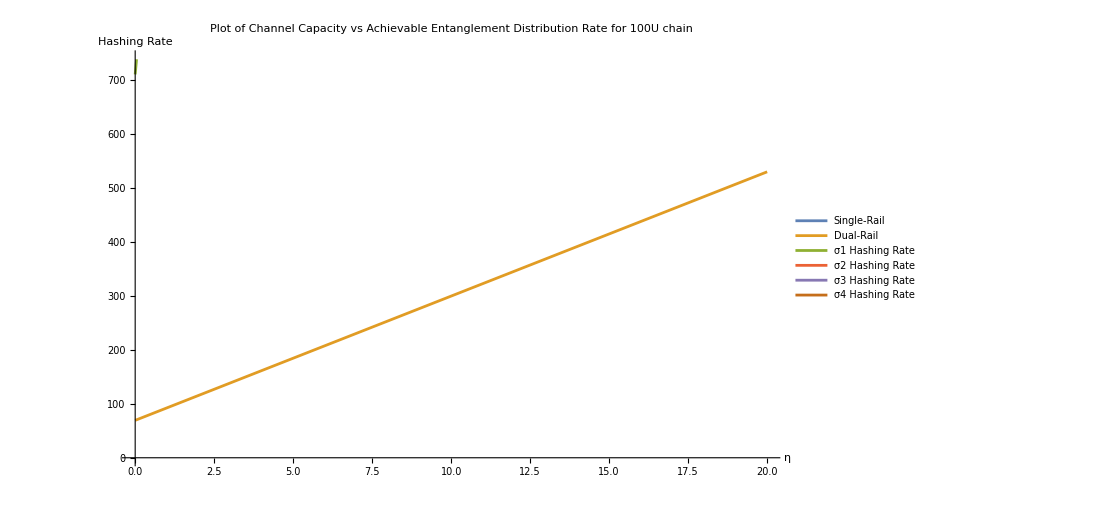

```mathematica
ListPlot[{SRhasingrate100 , DRhashingrate100tab ,hashingrate100σ1η , hashingrate100σ2η , hashingrate100σ3η , hashingrate100σ4η} , PlotRange->All , AxesStyle->Thick , Joined->True ,AxesLabel->{Style["η",Directive[Black,16]], Style["Hashing Rate",Directive[Black,16]]} , PlotLabel-> Style["Plot of Channel Capacity vs Achievable Entanglement Distribution Rate for 100U chain" , Directive[Black , 20]] , PlotLegends->{Style["Single-Rail" , Directive[Black , 16]] , Style["Dual-Rail" , Directive[Black , 16]],Style["σ1 Hashing Rate" , Directive[Black , 16]],Style["σ2 Hashing Rate" , Directive[Black , 16]],Style["σ3 Hashing Rate" , Directive[Black , 16]],Style["σ4 Hashing Rate" , Directive[Black , 16]]} , TicksStyle->Directive["Label", 14]]
```

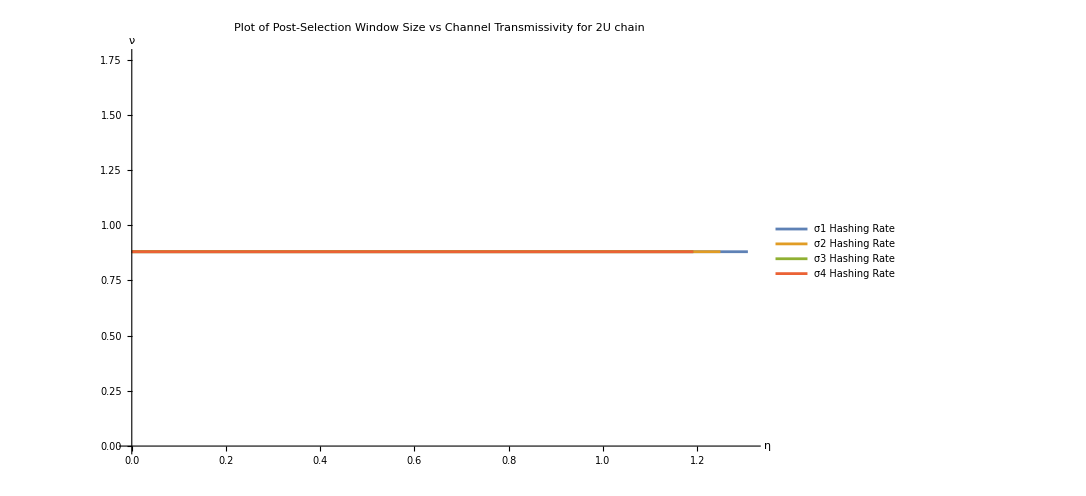

```mathematica
(*Investigating how size of post selection window changes as we vary channel transmissivity and the quality of the GKP qubits*)
ListPlot[{postselectiontable100σ1 , postselectiontable100σ2 , postselectiontable100σ3 , postselectiontable100σ4} , PlotRange->All , AxesStyle->Thick , Joined->True , AxesLabel->{Style["η",Directive[Black,16]], Style["ν",Directive[Black,16]]} , PlotLabel-> Style["Plot of Post-Selection Window Size vs Channel Transmissivity for 2U chain" , Directive[Black , 20]] , PlotLegends->{Style["σ1 Hashing Rate" , Directive[Black , 16]],Style["σ2 Hashing Rate" , Directive[Black , 16]],Style["σ3 Hashing Rate" , Directive[Black , 16]],Style["σ4 Hashing Rate" , Directive[Black , 16]]} , TicksStyle->Directive["Label", 14]]
```

```mathematica
DRhashingrate1tab = Table[{-10*Log10[η] , DRhashingrate1[η]} , {η , 0.01 , 1 , 0.01}];
DRhashingrate2tab = Table[{-10*Log10[η] , DRhashingrate2[η]} , {η , 0.01 , 1 , 0.01}];
DRhashingrate5tab = Table[{-10*Log10[η] , DRhashingrate5[η]} , {η , 0.01 , 1 , 0.01}];
DRhashingrate10tab = Table[{-10*Log10[η] , DRhashingrate10[η]} , {η , 0.01 , 1 , 0.01}];
DRhashingrate50tab = Table[{-10*Log10[η] , DRhashingrate50[η]} , {η , 0.01 , 1 , 0.01}];
DRhashingrate100tab = Table[{-10*Log10[η] , DRhashingrate100[η]} , {η , 0.01 , 1 , 0.01}];
```

```mathematica
(*Original Data*)

(*GKP*)
hashingrate1σ1ηOLD = Table[{10^{-hashingrateσ1η[[i , 1]]/10} , Exp[-hashingrateσ1η[[i , 2]]]} , {i , 1 , Length[hashingrateσ1η]}];
hashingrate1σ2ηOLD = Table[{10^{-hashingrateσ2η[[i , 1]]/10} , Exp[-hashingrateσ2η[[i , 2]]]} , {i , 1 , Length[hashingrateσ2η]}];
hashingrate1σ3ηOLD = Table[{10^{-hashingrateσ3η[[i , 1]]/10} , Exp[-hashingrateσ3η[[i , 2]]]} , {i , 1 , Length[hashingrateσ3η]}];
hashingrate1σ4ηOLD = Table[{10^{-hashingrateσ4η[[i , 1]]/10} , Exp[-hashingrateσ4η[[i , 2]]]} , {i , 1 , Length[hashingrateσ4η]}];

hashingrate2σ1ηOLD = Table[{10^{-hashingrate2σ1η[[i , 1]]/10} , Exp[-hashingrate2σ1η[[i , 2]]]} , {i , 1 , Length[hashingrate2σ1η]}];
hashingrate2σ2ηOLD = Table[{10^{-hashingrate2σ2η[[i , 1]]/10} , Exp[-hashingrate2σ2η[[i , 2]]]} , {i , 1 , Length[hashingrate2σ2η]}];
hashingrate2σ3ηOLD = Table[{10^{-hashingrate2σ3η[[i , 1]]/10} , Exp[-hashingrate2σ3η[[i , 2]]]} , {i , 1 , Length[hashingrate2σ3η]}];
hashingrate2σ4ηOLD = Table[{10^{-hashingrate2σ4η[[i , 1]]/10} , Exp[-hashingrate2σ4η[[i , 2]]]} , {i , 1 , Length[hashingrate2σ4η]}];

hashingrate5σ1ηOLD = Table[{10^{-hashingrate5σ1η[[i , 1]]/10} , Exp[-hashingrate5σ1η[[i , 2]]]} , {i , 1 , Length[hashingrate5σ1η]}];
hashingrate5σ2ηOLD = Table[{10^{-hashingrate5σ2η[[i , 1]]/10} , Exp[-hashingrate5σ2η[[i , 2]]]} , {i , 1 , Length[hashingrate5σ2η]}];
hashingrate5σ3ηOLD = Table[{10^{-hashingrate5σ3η[[i , 1]]/10} , Exp[-hashingrate5σ3η[[i , 2]]]} , {i , 1 , Length[hashingrate5σ3η]}];
hashingrate5σ4ηOLD = Table[{10^{-hashingrate5σ4η[[i , 1]]/10} , Exp[-hashingrate5σ4η[[i , 2]]]} , {i , 1 , Length[hashingrate5σ4η]}];

hashingrate10σ1ηOLD = Table[{10^{-hashingrate10σ1η[[i , 1]]/10} , Exp[-hashingrate10σ1η[[i , 2]]]} , {i , 1 , Length[hashingrate10σ1η]}];
hashingrate10σ2ηOLD = Table[{10^{-hashingrate10σ2η[[i , 1]]/10} , Exp[-hashingrate10σ2η[[i , 2]]]} , {i , 1 , Length[hashingrate10σ2η]}];
hashingrate10σ3ηOLD = Table[{10^{-hashingrate10σ3η[[i , 1]]/10} , Exp[-hashingrate10σ3η[[i , 2]]]} , {i , 1 , Length[hashingrate10σ3η]}];
hashingrate10σ4ηOLD = Table[{10^{-hashingrate10σ4η[[i , 1]]/10} , Exp[-hashingrate10σ4η[[i , 2]]]} , {i , 1 , Length[hashingrate10σ4η]}];

hashingrate50σ1ηOLD = Table[{10^{-hashingrate50σ1η[[i , 1]]/10} , Exp[-hashingrate50σ1η[[i , 2]]]} , {i , 1 , Length[hashingrate50σ1η]}];
hashingrate50σ2ηOLD = Table[{10^{-hashingrate50σ2η[[i , 1]]/10} , Exp[-hashingrate50σ2η[[i , 2]]]} , {i , 1 , Length[hashingrate50σ2η]}];
hashingrate50σ3ηOLD = Table[{10^{-hashingrate50σ3η[[i , 1]]/10} , Exp[-hashingrate50σ3η[[i , 2]]]} , {i , 1 , Length[hashingrate50σ3η]}];
hashingrate50σ4ηOLD = Table[{10^{-hashingrate50σ4η[[i , 1]]/10} , Exp[-hashingrate50σ4η[[i , 2]]]} , {i , 1 , Length[hashingrate50σ4η]}];

hashingrate100σ1ηOLD = Table[{10^{-hashingrate100σ1η[[i , 1]]/10} , Exp[-hashingrate100σ1η[[i , 2]]]} , {i , 1 , Length[hashingrate100σ1η]}];
hashingrate100σ2ηOLD = Table[{10^{-hashingrate100σ2η[[i , 1]]/10} , Exp[-hashingrate100σ2η[[i , 2]]]} , {i , 1 , Length[hashingrate100σ2η]}];
hashingrate100σ3ηOLD = Table[{10^{-hashingrate100σ3η[[i , 1]]/10} , Exp[-hashingrate100σ3η[[i , 2]]]} , {i , 1 , Length[hashingrate100σ3η]}];
hashingrate100σ4ηOLD = Table[{10^{-hashingrate100σ4η[[i , 1]]/10} , Exp[-hashingrate100σ4η[[i , 2]]]} , {i , 1 , Length[hashingrate100σ4η]}];


(*SR*)

SRhashingrate1OLD = Table[{10^{-SRhashingrate1[[i , 1]]/10} , Exp[-SRhashingrate1[[i , 2]]]} , {i , 1 , Length[SRhashingrate1]}];SRhashingrate2OLD = Table[{10^{-SRhashingrate2[[i , 1]]/10} , Exp[-SRhashingrate2[[i , 2]]]} , {i , 1 , Length[SRhashingrate2]}];
SRhashingrate5OLD = Table[{10^{-SRhasingrate5[[i , 1]]/10} , Exp[-SRhasingrate5[[i , 2]]]} , {i , 1 , Length[SRhasingrate5]}];
SRhashingrate10OLD = Table[{10^{-SRhasingrate10[[i , 1]]/10} , Exp[-SRhasingrate10[[i , 2]]]} , {i , 1 , Length[SRhasingrate10]}];
SRhashingrate50OLD = Table[{10^{-SRhasingrate50[[i , 1]]/10} , Exp[-SRhasingrate50[[i , 2]]]} , {i , 1 , Length[SRhashingrate50]}];
SRhashingrate100OLD = Table[{10^{-SRhasingrate100[[i , 1]]/10} , Exp[-SRhasingrate100[[i , 2]]]} , {i , 1 , Length[SRhasingrate100]}];

(*DR*)
DRhashingrate1OLD = Table[{10^{-DRhashingrate1tab[[i , 1]]/10} , Exp[-DRhashingrate1tab[[i , 2]]]} , {i , 1 , Length[DRhashingrate1tab]}];DRhashingrate2OLD = Table[{10^{-DRhashingrate2tab[[i , 1]]/10} , Exp[-DRhashingrate2tab[[i , 2]]]} , {i , 1 , Length[DRhashingrate2tab]}];
DRhashingrate5OLD = Table[{10^{-DRhashingrate5tab[[i , 1]]/10} , Exp[-DRhashingrate5tab[[i , 2]]]} , {i , 1 , Length[DRhashingrate5tab]}];
DRhashingrate10OLD = Table[{10^{-DRhashingrate10tab[[i , 1]]/10} , Exp[-DRhashingrate10tab[[i , 2]]]} , {i , 1 , Length[DRhashingrate10tab]}];
DRhashingrate50OLD = Table[{10^{-DRhashingrate50tab[[i , 1]]/10} , Exp[-DRhashingrate50tab[[i , 2]]]} , {i , 1 , Length[DRhashingrate50tab]}];
DRhashingrate100OLD = Table[{10^{-DRhashingrate100tab[[i , 1]]/10} , Exp[-DRhashingrate100tab[[i , 2]]]} , {i , 1 , Length[DRhashingrate100tab]}];
```